```mathematica
Clear["Global`*"];
```

```mathematica
data = Import["C:\\Users\\Matteo\\Desktop\\datap.txt","Table"]
```

{{83,934.2},{81,708.5},{79,518.9},{77,399.1},{75,278.3},{73,194.1},{71,134.5},{69,76.5},{67,50.1},{65,20.5},{63,12},{61,2.2},{59,0},{57,0},{55,2.29},{53,6.3},{51,8.1},{49,18.1},{47,22.2},{45,28.5},{43,33.1},{41,40.9},{39,45.7},{37,51.2},{35,53.6},{33,58.9},{31,64.8},{29,70},{27,72},{25,74},{23,76},{21,79},{19,81},{17,85},{15,86},{13,85},{11,87},{9,90}}

```mathematica
(*Da noi consideriamo 9 come primo punto NON fittabile. Ora, nella run P avevamo preso un dato in più (scorretto).
nella run S no. Se quindi correggiamo P con 9 (partendo dal penultimo dato, a 16°) e la run S sempre con 9 (stravolta dall'ultimo dato visto che è 16) => stiamo applicando
un deltaTheta di 7 e i conti tornano.*)
```

```mathematica
rp2[n1_, n2_, tiDeg_, I0_, deltat_] := (
ti = (tiDeg -deltat) / 180 * Pi;
tt= ArcSin[n1/n2 * Sin[ti]];
rp = (n1 *Cos[tt] - n2* Cos[ti]) / (n1* Cos[tt] + n2* Cos[ti]);
I0 * (rp ^ 2)
)
```

```mathematica
fit = NonlinearModelFit[
data,
{rp2[1, n2, t, I0, 0],  1.40 < n2 < 1.6 && I0 > 800},
{
{n2, 1.5}, I0
},
t
]
```

FittedModel[(2551.51 (-1.493 Cos[(π t)/180]+√(1-«17» («1»)^2))^2)/(1.493 Cos[(π t)/180]+√(1-0.448621 «1»))^2]

```mathematica
fit["ParameterErrors"]
fit["BestFitParameters"]
```

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{0.00599703,12.2534}

{n2→1.493,I0→2551.51}

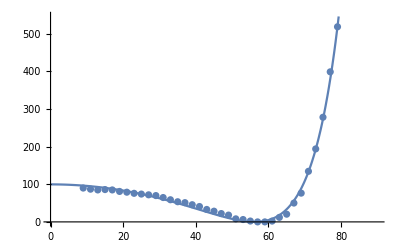

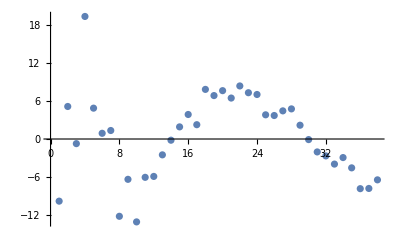

16.776

```mathematica
fittedFunc[t_] := rp2[1, n2, t, I0, 0] /. fit["BestFitParameters"]; 
p1 = Plot[fittedFunc[t],{t, 0, 90}];
p2 = ListPlot[data]; 
Show[p1, p2]
ListPlot[fit["FitResiduals"]]
Total[fit["FitResiduals"]^2] / 100
```